```mathematica
(* calculate the free gas scattering kernel *)

mn=939.565560 10^6;
hbar=6.582119 10^-16;
cspeed=299792458;
kB=8.617343 10^-5;
mA=10;
temp=10;
barn=1.*10^-28;

kn[e1_,e2_,mu_]:=Sqrt[2*mn*(e1+e2-2*mu*Sqrt[e1*e2])]/(hbar*cspeed);
chi[t_,te_,k_]:=Exp[-(k*k/(2*mA*mn))*(kB*te*t*t/hbar-ⅈ*t)*(hbar*cspeed*cspeed)];

sigma[e1_,e2_,mu_]:=(1/(4π))*(1/(2π))*Sqrt[e2/e1]*Integrate[Exp[-ⅈ*(e1-e2)*t/hbar]*chi[t,temp,kn[e1,e2,mu]],{t,-Infinity, Infinity}];

sigmaR[e1_,e2_,k_]:=(1/(4π))*(1/(2π))*Sqrt[e2/e1]*Sqrt[2*π*mA*mn/(temp*kB*k*k*cspeed*cspeed)]*Exp[-(mA*mn/(2*kB*temp*k*k*cspeed*cspeed))*(   ((e1-e2)/hbar-k*k*cspeed*cspeed*hbar/(2*mA*mn) ))^2];

sigmaS[e1_,e2_,mu_]:=FullSimplify[sigma[e1,e2,mu]];
sigmaSS[e1_,e2_,mu_]:=sigmaR[e1,e2,kn[e1,e2,mu]];
sigmaSE[e1_,e2_]:=2*π*NIntegrate[sigmaS[e1,e2,mu],{mu,-1,0.99}];
sigmaSSE[e1_,e2_]:=2*π*NIntegrate[sigmaSS[e1,e2,mu],{mu,-1,0.99}];

sigmaS[0.025,0.0025,0.5]
```

2.66708×10^-42+0. ⅈ

```mathematica
sigmaSE[0.025,0.0025]
```

5.47994×10^-15-2.4321×10^-31 ⅈ

```mathematica
sigmaSS[0.025,0.0025,0.5]
```

2.06742×10^-16

```mathematica
sigmaSSE[0.025,0.0025]
```

2.22198×10^-15

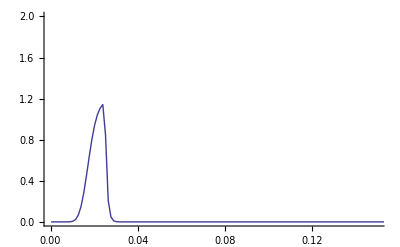

```mathematica
TablXS={};
NK=200;
e1=0.00025;
e2=0.25;
For[j=0,j≤NK,j++,AppendTo[TablXS,{e1+j*(e2-e1)/NK,sigmaSSE[0.025,e1+j*(e2-e1)/NK]/sigmaSSE[0.025,0.025]}]];
ListPlot[TablXS,Joined->True,PlotRange->{{0,0.15},{0,2}}]
```

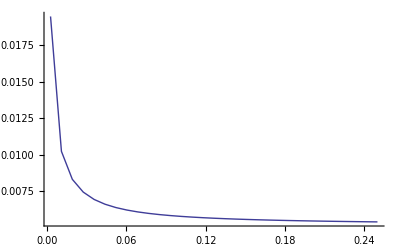

```mathematica
sigmaT[e_]:=NIntegrate[sigmaSS[e,x,mu]/sigmaSSE[0.025,0.025],{x,0,Infinity},{mu,-1,0.99}];
TablXST={};
NKS=30;
For[j=0,j≤NKS,j++,AppendTo[TablXST,{e1+j*(e2-e1)/NKS,sigmaT[e1+j*(e2-e1)/NKS]}]];
ListPlot[TablXST,Joined->True]
```